### Illustration of linear discriminant analysis

Let’s generate data with two features:

```mathematica
data=RandomVariate[ProductDistribution[NormalDistribution[1,1],NormalDistribution[1,1]],1000];
data2=RandomVariate[ProductDistribution[NormalDistribution[-1,1],NormalDistribution[-1,1]],1000];
```

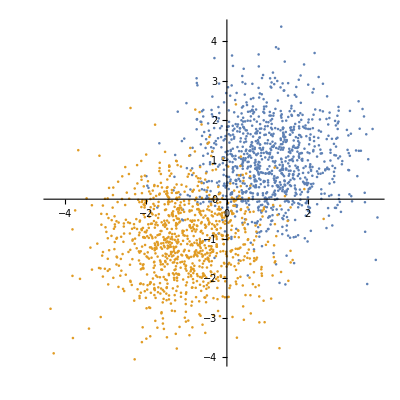

```mathematica
ListPlot[{data,data2},AspectRatio->1]
```

We want to classify this using linear discriminant analysis

Calculate means and covariance from these data sets:

```mathematica
μ0=Sum[data[[i]],{i,1,Length[data]}]/Length[data]
μ1=Sum[data2[[i]],{i,1,Length[data2]}]/Length[data2]
```

{1.03567,0.97435}

{-1.03395,-1.03116}

Covariance

```mathematica
Σ0=Sum[{{(data[[i,1]]-μ0[[1]])^2,(data[[i,1]]-μ0[[1]])(data[[i,2]]-μ0[[2]])},{(data[[i,1]]-μ0[[1]])(data[[i,2]]-μ0[[2]]),(data[[i,2]]-μ0[[2]])^2}},{i,1,Length[data]}]/Length[data]
Σ1=Sum[{{(data2[[i,1]]-μ1[[1]])^2,(data2[[i,1]]-μ1[[1]])(data2[[i,2]]-μ1[[2]])},{(data2[[i,1]]-μ1[[1]])(data2[[i,2]]-μ1[[2]]),(data2[[i,2]]-μ1[[2]])^2}},{i,1,Length[data2]}]/Length[data2]
```

{{0.917495,-0.00543106},{-0.00543106,0.974447}}

{{1.03835,0.0204218},{0.0204218,1.00165}}

We can now take a look at establishing the threshold. The LHS is given by:

```mathematica
ps[x_]:=(x-μ0).Inverse[Σ0].(x-μ0)+Log[Det[Σ0]]-((x-μ1).Inverse[Σ1].(x-μ1)+Log[Det[Σ1]])
```

A histogram for our data set from above looks like:

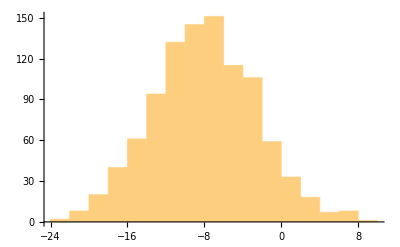

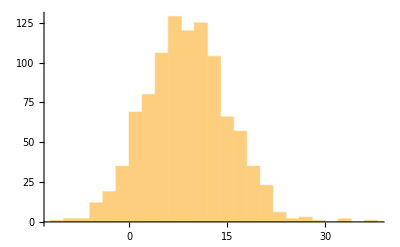

```mathematica
Histogram[Table[ps[data[[i]]],{i,1,Length[data]}]]
Histogram[Table[ps[data2[[i]]],{i,1,Length[data]}]]
```

For instance by taking the mean of these data sets we can come up with a threshold.

```mathematica
Sum[ps[data[[i]]],{i,1,Length[data]}]/Length[data]
Sum[ps[data2[[i]]],{i,1,Length[data2]}]/Length[data2]
(Sum[ps[data[[i]]],{i,1,Length[data]}]/Length[data]+Sum[ps[data2[[i]]],{i,1,Length[data2]}]/Length[data2])/2
```

-7.98911

8.8558

0.433345